# Expansion of Ẑ in q

## Set-up based on a paper

```mathematica
Z[r_,K_]:=Sum[q^(1/2 𝒹[K].𝒸[K,r].𝒹[K]+A[K,r])(q-q^(2 r+2 r 𝒹[K].𝓃[K])-q^(2+2𝒹[K].𝓃[K])+q^(3+2 r+2(1+r)𝒹[K].𝓃[K]))(-1)^(𝒹[K].𝓉[K])q^(𝒹[K].ℓ[K,r])/(pochhammer[q,𝒹[K]]/.List[a__]:>Times[a]),Evaluate[Table[{d[i],0,inf},{i,1,Length[𝓉[K]]}]/.List_[a___]:>a]]
η[q_]:=q^(1/24)Product[1-q^i,{i,1,∞}]
Ψ[m_,r_]:=Sum[Sign[k]q^(k^2/4/m)KroneckerDelta[Mod[k,2m]-Mod[r,2m]],{k,-20inf,20inf}]
```

```mathematica
pochhammer[a_,b_]:=QPochhammer[a,q,b]
𝒸[K_,r_]:=𝒸K[K]+2 r Em[K]
A[K_,r_]:=AK[K]+r/4+1/4/r-3/2+r c[r]^2
ℓ[K_,r_]:=ℓK[K]+(r-2+2 r c[r])Table[1,{i,1,Length[𝒸K[K]]}]
𝓃[K_]:=Table[1,{i,1,Length[𝒸K[K]]}]
Em[K_]:=KroneckerProduct[𝓃[K],𝓃[K]]
𝒹[K_]:=Table[d[i],{i,1,Length[𝒸K[K]]}]
```

Note: Z[r,K] is multiplies by Dedekind eta function η[q]. To reach the desired result we should consider Z[r,K]/η[q]!

## Results:

## 3_1knot

```mathematica
𝒸K[31]={{0,1,0,0},{1,0,1,0},{0,1,1,0},{0,0,0,1}};
AK[31]:=0
𝓉[31]={0,0,1,1};
ℓK[31]={1,2,3/2,3/2};
inf=7;
c[r_]:=0
```

```mathematica
Series[Z[1,31],{q,0,20}]
```

1-q-q^5+q^10-q^11+q^18+O[q]^21

```mathematica
Series[Z[2,31],{q,0,33}]/q^(1/8)
```

1-q-q^11+q^16-q^23+q^30+O[q]^33

```mathematica
Series[Z[3,31],{q,0,44}]/q^(1/3)
```

1-q-q^17+q^22-q^35+q^42+O[q]^44

These results are the same as page 83.

## 4_1knot

```mathematica
𝒸K[41]={{0,0,0,0,0,0},{0,0,-1,-1,0,0},{0,-1,0,0,1,0},{0,-1,0,1,1,0},{0,0,1,1,1,0},{0,0,0,0,0,1}};
AK[41]:=0
𝓉[41]={0,0,0,1,1,1};
ℓ[41,r_]={r-1,r-1,r-1,r-1/2,r-1/2,r-1/2};
inf=4;
c[r_]:=0
```

```mathematica
Series[Z[2,41]/q^(1/8),{q,0,20}]
```

1-q+2 q^3-2 q^6+q^9+3 q^10+q^11-q^14-3 q^15-q^16+2 q^19+2 q^20+O[q]^(161/8)

Overall factor is different (page 86) .

```mathematica
inf=9
```

7

```mathematica
ans1=Series[Z[2,41]/q^(1/8)q^(1/24)/η[q],{q,0,100}];
```

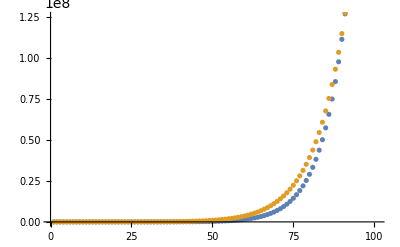

```mathematica
ListPlot[{Select[ans1[[3]],#>0&],Table[Exp[ 2π Sqrt[n/6/1.7]],{n,0,100}]}]
```

## False Theta function:

```mathematica
Zz[31,r_]:=1/η[q](Ψ[36 r +6,6r-5]-Ψ[36 r +6,6r+7]-Ψ[36 r +6,30r-1]+Ψ[36 r +6,30r+11])
```

```mathematica
Zz[31,1]/q^(1/168)//Simplify
```

(1-q-q^5+q^10-q^11+q^18+q^30-q^41+q^43-q^56-q^76+q^93-q^96+q^115)/(q^(1/24) QPochhammer[q,q])

```mathematica
inf=14
```

14

```mathematica
Series[Z[1,31],{q,0,116}]
```

1-q-q^5+q^10-q^11+q^18+q^30-q^41+q^43-q^56-q^76+q^93-q^96+q^115+O[q]^117

# growth

```mathematica
Z[r_,K_]:=Sum[q^(1/2 𝒹[K].𝒸[K,r].𝒹[K]+A[K,r])(q-q^(2 r+2 r 𝒹[K].𝓃[K])-q^(2+2𝒹[K].𝓃[K])+q^(3+2 r+2(1+r)𝒹[K].𝓃[K]))(-1)^(𝒹[K].𝓉[K])q^(𝒹[K].ℓ[K,r])/(pochhammer[q,𝒹[K]]/.List[a__]:>Times[a]),Evaluate[Table[{d[i],0,inf},{i,1,Length[𝓉[K]]}]/.List_[a___]:>a]]
```

```mathematica
summand[r_,K_]:=q^(1/2 𝒹[K].𝒸[K,r].𝒹[K]+A[K,r])(q-q^(2 r+2 r 𝒹[K].𝓃[K])-q^(2+2𝒹[K].𝓃[K])+q^(3+2 r+2(1+r)𝒹[K].𝓃[K]))(-1)^(𝒹[K].𝓉[K])q^(𝒹[K].ℓ[K,r])/(pochhammer[q,𝒹[K]]/.List[a__]:>Times[a])
```

```mathematica
inf=5
```

5

```mathematica
IdentityMatrix[4]
```

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
a:=RandomInteger[{0,1}]
```

```mathematica
matrix:=Table[Table[a,4],4]
```

```mathematica
matrix+Transpose[matrix]//InputForm
```

{{0, -2, -3, -1}, {2, -1, -3, 0}, {0, -2, 0, 1}, {0, -1, -1, 1}}

```mathematica
𝒸K[test]:=matrix+Transpose[matrix];
AK[test]:=0
𝓉[test]={0,0,1,1};
ℓK[test]={1,2,3/2,3/2};
inf=7;
c[r_]:=0
```

```mathematica
inf=7
```

7

```mathematica
𝒸K[31]//MatrixForm
```

(0 | 1 | 0 | 0
1 | 0 | 1 | 0
0 | 1 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
ans={Series[Z[2,test]/q^(1/8),{q,0,20}],𝒸K[test]//MatrixForm}
```

{1-q-q^3+q^(7/2)+q^6-q^(13/2)-q^(21/2)+q^11+3 q^12-q^(25/2)+4 q^13-4 q^(27/2)+6 q^14-6 q^(29/2)+8 q^15-7 q^(31/2)+9 q^16-10 q^(33/2)+9 q^17-11 q^(35/2)+10 q^18-10 q^(37/2)+10 q^19-10 q^(39/2)+10 q^20+O[q]^(161/8),(1 | 0 | 1 | 1
0 | 1 | 0 | 0
0 | 0 | 1 | 0
2 | 0 | 2 | 2)}

```mathematica
ans
```

1-q+q^(5/2)+q^(7/2)+2 q^(9/2)+q^(11/2)+2 q^6+q^(13/2)+4 q^7+8 q^8+12 q^9-q^(19/2)+15 q^10+O[q]^(81/8)

```mathematica
FindFit[Select[ans[[3]],#!=0&], a x^b,{a,b},x]
```

{a→-0.00260289,b→0.175032}

```mathematica
FindFit[%88[[3]], x^b,{b},x]
```

{b→1.72442}

```mathematica
ListLinePlot[Select[ans[[3]],#!=0&]]
```

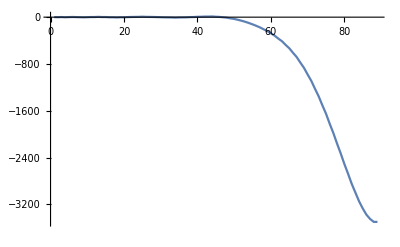

```mathematica
ListLinePlot[Select[ans[[3]],#!=0&]]
```

```mathematica
Series[summand[1,31]/.d[A__]:>number,{q,0,3}]
```

q^(2 number+19 number^2) (-2 q^(2+8 number)+q^(5+16 number)+(q+O[q]^4)) (1+q^(3 number) O[q]^5+q^(4 number) O[q]^5+q^(5 number) O[q]^5+q^(2 number) (q^3+O[q]^4)+q^number (-q-q^2-q^3+O[q]^4))^4 ((-1)^(2 number)/q+4 (-1)^(2 number)+14 (-1)^(2 number) q+40 (-1)^(2 number) q^2+105 (-1)^(2 number) q^3+O[q]^4)

```mathematica
pochhammer[q,2]
```

QPochhammer[q,q,2]

```mathematica
η[q]
```

q^(1/24) QPochhammer[q,q]